```mathematica
m = e l^-2 t^2;
```

```mathematica
(t^2 q^2)/(m l^3)
```

q^2/(e l)

```mathematica
l m q^2
```

(e q^2 t^2)/l

```mathematica
(m l^2)/t
```

e t

```mathematica
l^3/(m t^2)
```

l^5/(e t^4)

```mathematica
m l^-3
```

(e t^2)/l^5

```mathematica
m t^-2
```

e/l^2

```mathematica
q^-1 l^2 m t^-2
```

```mathematica
e/q
```

```mathematica
m l q^-1 t^-2
```

e/(l q)

```mathematica
q^2 l^-2 m^-1 t^2
```

q^2/e

```mathematica
m t^-1 q^-1
```

(e t)/(l^2 q)

```mathematica
m l t^-1 q^-1
```

(e t)/(l q)

```mathematica
m t^-2
```

e/l^2

```mathematica
m l^-1 t^-2
```

e/l^3

```mathematica
m l^2 t^-1 q^-2
```

(e t)/q^2

```mathematica
RegionCentroid[Rectangle[{0,0},{2,1-4}]]
```

{1,-3/2}

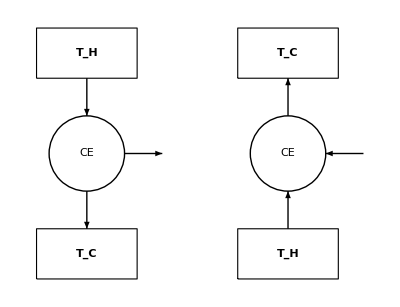

```mathematica
img=Graphics[{
EdgeForm[Thick],
Text[Style["T_H",Large,Bold],{1,0.5}],
Text[Style["T_C",Large,Bold],{1,-7/2}],
Opacity[0],Rectangle[{0,0},{2,1}],
Opacity[1],Thick,Arrow[{{1,0},{1,-3/2+0.75}}],
Opacity[1],Thick,Circle[{1,-3/2},0.75],
Text[Style["CE",Large],{1,-3/2}],
Opacity[1],Thick,Arrow[{{1.75,-3/2},{1.75+0.75,-3/2}}],
Arrow[{{1,-3/2-0.75},{1,-3}}],
Opacity[0],Rectangle[{0,-4},{2,1-4}],
Opacity[1],
Text[Style["T_C",Large,Bold],{1+4,0.5}],
Text[Style["T_H",Large,Bold],{1+4,-7/2}],
Opacity[0],Rectangle[{0+4,0},{2+4,1}],
Opacity[1],Thick,Arrow[{{1+4,-3/2+0.75},{1+4,0}}],
Opacity[1],Thick,Circle[{1+4,-3/2},0.75],
Text[Style["CE",Large],{1+4,-3/2}],
Opacity[1],Thick,Arrow[{{1.75+0.75+4,-3/2},{1.75+4,-3/2}}],
Arrow[{{1+4,-3},{1+4,-3/2-0.75}}],
Opacity[0],Rectangle[{0+4,-4},{2+4,1-4}]}]
```

```mathematica
EuclideanDistance[{1,0},{1,-3/2+0.75}]
```

0.75

```mathematica
Export["~/school/FA22/PHYS163a/figs/carnot.png",img]
```

~/school/FA22/PHYS163a/figs/carnot.png

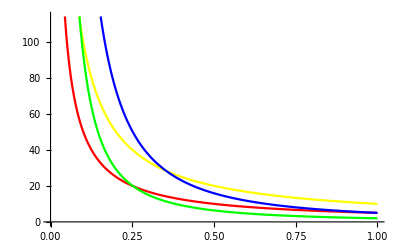

```mathematica
Plot[{5/(x),10/(x),2/x^(5/3),5/x^(5/3)}
,{x,0,1},PlotStyle->{Red, Yellow, Green, Blue}]
```

```mathematica
Y = 10/x;
R = 5/x;
G = 2/x^(5/3);
B=5/x^(5/3);
```

```mathematica
Solve[Y==G,x]//Simplify(*Crossover for first adiabat*)
Solve[Y==B,x]//Simplify
```

{{x→1/(5 √5)}}

{{x→1/(2 √2)}}

```mathematica
Solve[G==Y,x]
Solve[G==R,x]
```

{{x→1/(5 √5)}}

{{x→(2 √(2/5))/5}}

```mathematica
Solve[R==G,x]
Solve[R==B,x]
```

{{x→(2 √(2/5))/5}}

{{x→1}}

```mathematica
Solve[B==R,x]
Solve[B==Y,x]
```

{{x→1}}

{{x→1/(2 √2)}}

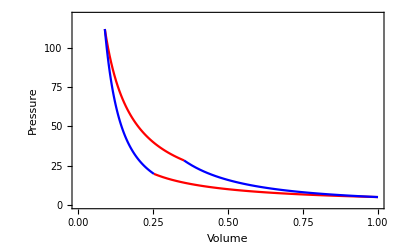

```mathematica
cycle = Show[
Plot[R,{x,2/5 √(2/5),1},PlotStyle->Red],
Plot[Y,{x,1/(5 √5),1/(2 √2)},PlotStyle->Red],
Plot[G,{x,1/(5 √5),2/5 √(2/5)},PlotStyle->Blue],
Plot[B,{x,1/(2 √2),1},PlotStyle->Blue],
PlotRange->{{0,1.0},{0,120}},
Axes->False,
AxesLabel->{"Volume","Pressure"},
Frame->True,
FrameLabel->{"Volume","Pressure"},
FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]]
```

```mathematica
Export["~/school/FA22/PHYS163a/figs/carnotcycle.png",cycle]
```

~/school/FA22/PHYS163a/figs/carnotcycle.png

```mathematica
Clear[m]
```

```mathematica
F=m l t^-2
```

(l m)/t^2

```mathematica
F*l^2*m^-2
```

l^3/(m t^2)

```mathematica
c = l/t;
h =(m l^2)/t;
G=l^3/(m t^2);
```

```mathematica
FullSimplify[Distribute[c^β h^α],Assumptions->{l,t,m,β,α}∈PositiveIntegers]
```

(l/t)^β ((l^2 m)/t)^α

```mathematica
TeXForm@((l^(3α)/(m^α t^(2α))) (l^β/t^β))
```

m^{-\alpha } l^{3 \alpha +\beta } t^{-2 \alpha -\beta }

```mathematica
(l^3/(m t^2))^α (l/t)^β/.{α->-1,β->2}
```

m/l

```mathematica
(l^(3β)/(m^β t^(2β))) (l^α/t^α)/.{α->β,β->α}
```

l^(3 α+β) m^-α t^(-2 α-β)

```mathematica
l^(α+3 β) m^-β t^(-α-2 β)/.β->0
```

l^α t^-α

```mathematica
Solve[{α+3β==-3,-β==1,-α-2β==0},{α,β}]
```

{}

```mathematica
((l^(3α)/(m^α t^(2α))) (l^β/t^β))/.{α->1,β->-2}
```

l/m

```mathematica
FullSimplify[Distribute[c^β h^α],Assumptions->{l,t,m,β,α}∈PositiveIntegers]
```

(l/t)^β ((l^2 m)/t)^α

```mathematica
(l^β/t^β) ((l^(2α) m^α)/t^α)
```

l^(2 α+β) m^α t^(-α-β)

```mathematica
(l^β/t^β) ((l^(2α) m^α)/t^α)/.{α->1,β->-1}
```

l m

```mathematica
ScientificForm[(1.0*10^-11)/((10^8)^2)]
```

1.×10^-27

```mathematica
(10^8)^2
```

10000000000000000

```mathematica
ScientificForm[N[10000000000000000,17]]
```

1.0000000000000000×10^16

```mathematica
Entity["PhysicalConstant","reduced Planck Constant"]
```

Entity[PhysicalConstant,reduced Planck Constant]

```mathematica
LinguisticAssistant
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

Missing[RetrievalFailure]